```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/SMS-stop-FA/SMS-stop-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## g-g- t- t (1-loop)

```mathematica
tops0 = CreateTopologies[0,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { V[4],V[4]} -> {F[9],-F[9]};
allDiags = InsertFields[Join[tops0,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8]}];
```

generic model {Lorentz} initialized

classes model {../../Models/SMS-stop-FA/SMS-stop-FA} initialized

in total: 47 Particles insertions

```mathematica
amp=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->True,DropSumOver->True,SMP->True,LorentzIndexNames-> {μ,ν},Contract->True,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings//.{GS->gs}),ChangeDimension->D]/.{GS->gs};
nonZero={};
(* Keep only the diagrams up to gs^2 and containing yDM *)
For[n=1,n≤Length[amp],++n,
	M = Take[amp,{n}];
	M = SUNSimplify[M];
	M=Normal[Series[M,{gs,0,2}]];
	M=Normal[Series[M,{yDM,0,2}]];
	M=DiracSimplify[M];
    If[!M==={0} && !FreeQ[M,yDM] ,AppendTo[nonZero,n]];
];
```

in total: 47 Particles amplitudes

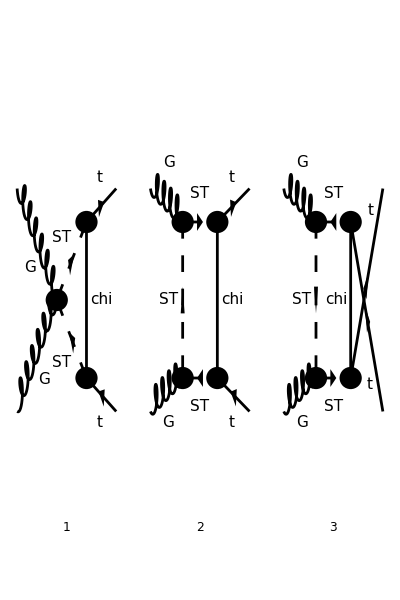

```mathematica
goodDiags=DiagramExtract[allDiags,nonZero];
(* goodDiags=DiagramExtract[goodDiags,{2,3,6,7,8,9}]; *)
goodDiags=DiagramExtract[goodDiags,{4,10,11}];
(* goodDiags=DiagramExtract[goodDiags,{4}]; *)
Paint[goodDiags,ColumnsXRows->{3,4},ImageSize->{ 400,600},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},LorentzIndexNames->{μ,ν},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]]
```

in total: 3 Particles amplitudes

-gs^2 yDM^2 ((γ·q).(γ̄)^6 ((g^μν ((T^Glu1 T^Glu2)_Col3Col4+(T^Glu2 T^Glu1)_Col3Col4))/((q^2-mChi^2).((p1+q)^2-mST^2).((p2-q)^2-mST^2))+(k2^ν+2 q^ν) (k2^μ-p1^μ-p2^μ+2 q^μ) (((T^Glu1 T^Glu2)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p2+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))-((T^Glu2 T^Glu1)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p1+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))))+(k2^ν+2 q^ν) (k2^μ-p1^μ-p2^μ+2 q^μ) ((((γ·k2).(γ̄)^6-(γ·p2).(γ̄)^6) (T^Glu1 T^Glu2)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p2+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))+(((γ·p1).(γ̄)^6-(γ·k2).(γ̄)^6) (T^Glu2 T^Glu1)_Col3Col4)/((q^2-mST^2).((k2+q)^2-mST^2).((k2-p1+q)^2-mChi^2).((k2-p1-p2+q)^2-mST^2))))

```mathematica
ampC =( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify);
```

```mathematica
ampEsimp=ExpandScalarProduct[DiracSimplify[ampC/.{DiracGamma[7]->1-DiracGamma[6]}]];
```

## On - Shell Case

since we are only interested in q q -> tt or gg -> tt, the t - t - g - g vertex only contributes when all external particles are on - shell, so we make use of this to simplify the final expressions

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,MT,MT,0,0];
```

```mathematica
ampEsimp2=Simplify[DiracSimplify[ampEsimp]]/.{s+t+u-> 2 MT^2};
```

## Check Divergences

```mathematica
Table[{Cases2[ampEsimp2,PaVe][[i]],PaXEvaluateUV[Cases2[ampEsimp2,PaVe][[i]]]},{i,1,Length[Cases2[ampEsimp2,PaVe]]}]
```

(C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2) | 0
D_1(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_1(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_2(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_2(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_3(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_3(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_00(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_00(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_11(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_11(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_12(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_12(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_13(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_13(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_22(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_22(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_23(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_23(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_33(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_33(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_001(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_001(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_002(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_002(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_003(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_003(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_111(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_111(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_112(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_112(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_113(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_113(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_122(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_122(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_123(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_123(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_133(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_133(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_222(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_222(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_223(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_223(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_233(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_233(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_333(0,t,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0
D_333(0,u,MT^2,s,MT^2,0,mST^2,mST^2,mChi^2,mST^2) | 0)

```mathematica
(* Divergences from loops *)
loopUV=FullSimplify[PaXEvaluateUV[ampEsimp2]];
(* Divergences from counter-terms *)
ctUV=FullSimplify[Coefficient[ampEsimp2,deltaCTR]] (-1/(4 EpsilonUV));
FullSimplify[loopUV+ctUV]
```

0

### Replace D - integrals by short names

```mathematica
PVsubs =Flatten[Table[PaVe[a,{0,b,MT^2,s,MT^2,0},{mST^2,mST^2,mChi^2,mST^2},c__]->ToExpression[StringJoin[ "D",ToString[a],"[",ToString[b],",s]" ]],{a,0,3},{b,{u,t}}]];
PVsubs=Join[PVsubs,Flatten[Table[PaVe[a1,a2,{0,b,MT^2,s,MT^2,0},{mST^2,mST^2,mChi^2,mST^2},c__]->ToExpression[StringJoin[ "D",ToString[a1],ToString[a2],"[",ToString[b],",s]"]],{a1,0,3},{a2,0,3},{b,{u,t}}]]];
PVsubs=Join[PVsubs,Flatten[Table[PaVe[a1,a2,a3,{0,b,MT^2,s,MT^2,0},{mST^2,mST^2,mChi^2,mST^2},c__]->ToExpression[StringJoin[ "D",ToString[a1],ToString[a2],ToString[a3],"[",ToString[b],",s]"]],{a1,0,3},{a2,0,3},{a3,0,3},{b,{u,t}}]]];
PVsubs = Join[PVsubs,{PaVe[1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2},c__]->C1[s,p1sq,p2sq],D0[0,MT^2,MT^2,0,t,s,mST^2,mST^2,mChi^2,mST^2]->D0[t,s],D0[0,MT^2,MT^2,0,u,s,mST^2,mST^2,mChi^2,mST^2]->D0[u,s]}];
```

#### Check replacements

```mathematica
Table[{Cases2[ampEsimp2,PaVe][[i]],Cases2[ampEsimp2,PaVe][[i]]/.PVsubs},{i,1,Length[Cases2[ampEsimp2,PaVe]]}];
```

```mathematica
ampEsimp3=Simplify[ampEsimp2/.PVsubs];
```

```mathematica
spinorChains1=Tally[Cases[{ampEsimp3},DiracGamma[___],All]][[All,1]]
spinorChains2=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___],All]][[All,1]]
spinorChains3=Tally[Cases[{ampEsimp3},DiracGamma[___].DiracGamma[___].DiracGamma[___],All]][[All,1]]
allTerms=Sort[Join[spinorChains1,spinorChains2]];
pairs1=Cases2[ampEsimp3,Pair]
su3prods=Join[Cases2[ampEsimp3,SUNTF],Cases2[ampEsimp3,SUNF]]
pairs2=Flatten[Table[pairs1[[i]] pairs1[[j]],{i,1,Length[pairs1]},{j,i+1,Length[pairs1]}]];
allPairs=Join[pairs1,pairs2];
```

{γ·k2,(γ̄)^6,γ·p2,γ^ν,γ^μ,γ·p1}

{(γ·k2).(γ̄)^6,(γ·p2).(γ̄)^6,γ^ν.(γ̄)^6,γ^μ.(γ̄)^6,(γ·p1).(γ̄)^6}

{}

{g^μν,k2^μ,p1^μ,p2^μ,k2^ν,p1^ν,p2^ν}

{(T^Glu1 T^Glu2)_Col3Col4,(T^Glu2 T^Glu1)_Col3Col4}

### Coefficients for each term

```mathematica
su3Terms={};
Do[c=FullSimplify[Coefficient[Coefficient[Coefficient[Expand[ampEsimp3],su3prods[[i]]],allTerms[[j]]],allPairs[[k]]]];
If[c==0,Continue[]];
If[Count[c,LorentzIndex[μ,D],Infinity]≠0,Continue[]];
If[Count[c,LorentzIndex[ν,D],Infinity]≠0,Continue[]];
c= Simplify[c/(I Pi^2 gs^2 yDM^2)];
AppendTo[su3Terms,{su3prods[[i]],allTerms[[j]],allPairs[[k]],c}];
,{i,1,Length[su3prods]},{j,1,Length[allTerms]},{k,1,Length[allPairs]}];
```

#### Check that all terms have been correctly split

```mathematica
ampTot = I Pi^2 gs^2 yDM^2 Sum[su3Terms[[i,1]] su3Terms[[i,2]] su3Terms[[i,3]]su3Terms[[i,4]],{i,1,Length[su3Terms]}];
Simplify[ampTot-ampEsimp3]
```

0

```mathematica
su3Terms
```

((T^Glu1 T^Glu2)_Col3Col4 | γ^μ.(γ̄)^6 | k2^ν | 2 (D00(t,s)+2 D001(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | γ^μ.(γ̄)^6 | p1^ν | 4 D003(t,s)
(T^Glu1 T^Glu2)_Col3Col4 | γ^μ.(γ̄)^6 | p2^ν | 4 (D002(t,s)+D003(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | γ^ν.(γ̄)^6 | k2^μ | 2 (D00(t,s)+2 D001(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | γ^ν.(γ̄)^6 | p1^μ | 2 (D00(t,s)+2 D003(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | γ^ν.(γ̄)^6 | p2^μ | 2 (D00(t,s)+2 (D002(t,s)+D003(t,s)))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·k2).(γ̄)^6 | g^μν | 4 D001(t,s)
(T^Glu1 T^Glu2)_Col3Col4 | (γ·k2).(γ̄)^6 | k2^μ k2^ν | D1(t,s)+4 (D11(t,s)+D111(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·k2).(γ̄)^6 | k2^μ p1^ν | 2 (2 D113(t,s)+D13(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·k2).(γ̄)^6 | k2^μ p2^ν | 2 (2 D112(t,s)+2 D113(t,s)+D12(t,s)+D13(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·k2).(γ̄)^6 | k2^ν p1^μ | D1(t,s)+2 (D11(t,s)+2 D113(t,s)+D13(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·k2).(γ̄)^6 | p1^μ p1^ν | 2 (D13(t,s)+2 D133(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·k2).(γ̄)^6 | p1^μ p2^ν | 2 (D12(t,s)+2 D123(t,s)+D13(t,s)+2 D133(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·k2).(γ̄)^6 | k2^ν p2^μ | D1(t,s)+2 (D11(t,s)+2 D112(t,s)+2 D113(t,s)+D12(t,s)+D13(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·k2).(γ̄)^6 | p1^ν p2^μ | 2 (2 D123(t,s)+D13(t,s)+2 D133(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·k2).(γ̄)^6 | p2^μ p2^ν | 2 (D12(t,s)+2 D122(t,s)+4 D123(t,s)+D13(t,s)+2 D133(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·p1).(γ̄)^6 | g^μν | 4 D003(t,s)-C1(s,p1sq,p2sq)
(T^Glu1 T^Glu2)_Col3Col4 | (γ·p1).(γ̄)^6 | k2^μ k2^ν | 4 (D113(t,s)+D13(t,s))+D3(t,s)
(T^Glu1 T^Glu2)_Col3Col4 | (γ·p1).(γ̄)^6 | k2^μ p1^ν | 2 (2 D133(t,s)+D33(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·p1).(γ̄)^6 | k2^μ p2^ν | 2 (2 D123(t,s)+2 D133(t,s)+D23(t,s)+D33(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·p1).(γ̄)^6 | k2^ν p1^μ | 2 D13(t,s)+4 D133(t,s)+D3(t,s)+2 D33(t,s)
(T^Glu1 T^Glu2)_Col3Col4 | (γ·p1).(γ̄)^6 | p1^μ p1^ν | 2 (D33(t,s)+2 D333(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·p1).(γ̄)^6 | p1^μ p2^ν | 2 (D23(t,s)+2 D233(t,s)+D33(t,s)+2 D333(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·p1).(γ̄)^6 | k2^ν p2^μ | 4 D123(t,s)+2 D13(t,s)+4 D133(t,s)+2 D23(t,s)+D3(t,s)+2 D33(t,s)
(T^Glu1 T^Glu2)_Col3Col4 | (γ·p1).(γ̄)^6 | p1^ν p2^μ | 2 (2 D233(t,s)+D33(t,s)+2 D333(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·p1).(γ̄)^6 | p2^μ p2^ν | 2 (2 D223(t,s)+D23(t,s)+4 D233(t,s)+D33(t,s)+2 D333(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·p2).(γ̄)^6 | g^μν | C1(s,p1sq,p2sq)+4 (D00(t,s)+D002(t,s)+D003(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·p2).(γ̄)^6 | k2^μ k2^ν | D0(t,s)+4 D1(t,s)+4 D11(t,s)+4 D112(t,s)+4 D113(t,s)+4 D12(t,s)+4 D13(t,s)+D2(t,s)+D3(t,s)
(T^Glu1 T^Glu2)_Col3Col4 | (γ·p2).(γ̄)^6 | k2^μ p1^ν | 2 (2 D123(t,s)+2 D13(t,s)+2 D133(t,s)+D23(t,s)+D3(t,s)+D33(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·p2).(γ̄)^6 | k2^μ p2^ν | 2 (2 D12(t,s)+2 D122(t,s)+4 D123(t,s)+2 D13(t,s)+2 D133(t,s)+D2(t,s)+D22(t,s)+2 D23(t,s)+D3(t,s)+D33(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·p2).(γ̄)^6 | k2^ν p1^μ | D0(t,s)+2 D1(t,s)+2 D12(t,s)+4 D123(t,s)+6 D13(t,s)+4 D133(t,s)+D2(t,s)+2 D23(t,s)+3 D3(t,s)+2 D33(t,s)
(T^Glu1 T^Glu2)_Col3Col4 | (γ·p2).(γ̄)^6 | p1^μ p1^ν | 2 (D23(t,s)+2 D233(t,s)+D3(t,s)+3 D33(t,s)+2 D333(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·p2).(γ̄)^6 | p1^μ p2^ν | 2 (D2(t,s)+D22(t,s)+2 D223(t,s)+4 D23(t,s)+4 D233(t,s)+D3(t,s)+3 D33(t,s)+2 D333(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·p2).(γ̄)^6 | k2^ν p2^μ | D0(t,s)+2 D1(t,s)+6 D12(t,s)+4 D122(t,s)+8 D123(t,s)+6 D13(t,s)+4 D133(t,s)+3 D2(t,s)+2 D22(t,s)+4 D23(t,s)+3 D3(t,s)+2 D33(t,s)
(T^Glu1 T^Glu2)_Col3Col4 | (γ·p2).(γ̄)^6 | p1^ν p2^μ | 2 (2 D223(t,s)+3 D23(t,s)+4 D233(t,s)+D3(t,s)+3 D33(t,s)+2 D333(t,s))
(T^Glu1 T^Glu2)_Col3Col4 | (γ·p2).(γ̄)^6 | p2^μ p2^ν | 2 (D2(t,s)+3 D22(t,s)+2 D222(t,s)+6 D223(t,s)+6 D23(t,s)+6 D233(t,s)+D3(t,s)+3 D33(t,s)+2 D333(t,s))
(T^Glu2 T^Glu1)_Col3Col4 | γ^μ.(γ̄)^6 | k2^ν | -2 (D00(u,s)+2 D001(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | γ^μ.(γ̄)^6 | p1^ν | -4 (D002(u,s)+D003(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | γ^μ.(γ̄)^6 | p2^ν | -4 D003(u,s)
(T^Glu2 T^Glu1)_Col3Col4 | γ^ν.(γ̄)^6 | k2^μ | -2 (D00(u,s)+2 D001(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | γ^ν.(γ̄)^6 | p1^μ | -2 (D00(u,s)+2 (D002(u,s)+D003(u,s)))
(T^Glu2 T^Glu1)_Col3Col4 | γ^ν.(γ̄)^6 | p2^μ | -2 (D00(u,s)+2 D003(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·k2).(γ̄)^6 | g^μν | -4 D001(u,s)
(T^Glu2 T^Glu1)_Col3Col4 | (γ·k2).(γ̄)^6 | k2^μ k2^ν | -D1(u,s)-4 (D11(u,s)+D111(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·k2).(γ̄)^6 | k2^μ p1^ν | -2 (2 D112(u,s)+2 D113(u,s)+D12(u,s)+D13(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·k2).(γ̄)^6 | k2^μ p2^ν | -2 (2 D113(u,s)+D13(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·k2).(γ̄)^6 | k2^ν p1^μ | -D1(u,s)-2 (D11(u,s)+2 D112(u,s)+2 D113(u,s)+D12(u,s)+D13(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·k2).(γ̄)^6 | p1^μ p1^ν | -2 (D12(u,s)+2 D122(u,s)+4 D123(u,s)+D13(u,s)+2 D133(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·k2).(γ̄)^6 | p1^μ p2^ν | -2 (2 D123(u,s)+D13(u,s)+2 D133(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·k2).(γ̄)^6 | k2^ν p2^μ | -D1(u,s)-2 (D11(u,s)+2 D113(u,s)+D13(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·k2).(γ̄)^6 | p1^ν p2^μ | -2 (D12(u,s)+2 D123(u,s)+D13(u,s)+2 D133(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·k2).(γ̄)^6 | p2^μ p2^ν | -2 (D13(u,s)+2 D133(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·p1).(γ̄)^6 | g^μν | -C1(s,p1sq,p2sq)-4 (D00(u,s)+D002(u,s)+D003(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·p1).(γ̄)^6 | k2^μ k2^ν | -D0(u,s)-4 D1(u,s)-4 D11(u,s)-4 D112(u,s)-4 D113(u,s)-4 D12(u,s)-4 D13(u,s)-D2(u,s)-D3(u,s)
(T^Glu2 T^Glu1)_Col3Col4 | (γ·p1).(γ̄)^6 | k2^μ p1^ν | -2 (2 D12(u,s)+2 D122(u,s)+4 D123(u,s)+2 D13(u,s)+2 D133(u,s)+D2(u,s)+D22(u,s)+2 D23(u,s)+D3(u,s)+D33(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·p1).(γ̄)^6 | k2^μ p2^ν | -2 (2 D123(u,s)+2 D13(u,s)+2 D133(u,s)+D23(u,s)+D3(u,s)+D33(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·p1).(γ̄)^6 | k2^ν p1^μ | -D0(u,s)-2 D1(u,s)-6 D12(u,s)-4 D122(u,s)-8 D123(u,s)-6 D13(u,s)-4 D133(u,s)-3 D2(u,s)-2 D22(u,s)-4 D23(u,s)-3 D3(u,s)-2 D33(u,s)
(T^Glu2 T^Glu1)_Col3Col4 | (γ·p1).(γ̄)^6 | p1^μ p1^ν | -2 (D2(u,s)+3 D22(u,s)+2 D222(u,s)+6 D223(u,s)+6 D23(u,s)+6 D233(u,s)+D3(u,s)+3 D33(u,s)+2 D333(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·p1).(γ̄)^6 | p1^μ p2^ν | -2 (2 D223(u,s)+3 D23(u,s)+4 D233(u,s)+D3(u,s)+3 D33(u,s)+2 D333(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·p1).(γ̄)^6 | k2^ν p2^μ | -D0(u,s)-2 D1(u,s)-2 D12(u,s)-4 D123(u,s)-6 D13(u,s)-4 D133(u,s)-D2(u,s)-2 D23(u,s)-3 D3(u,s)-2 D33(u,s)
(T^Glu2 T^Glu1)_Col3Col4 | (γ·p1).(γ̄)^6 | p1^ν p2^μ | -2 (D2(u,s)+D22(u,s)+2 D223(u,s)+4 D23(u,s)+4 D233(u,s)+D3(u,s)+3 D33(u,s)+2 D333(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·p1).(γ̄)^6 | p2^μ p2^ν | -2 (D23(u,s)+2 D233(u,s)+D3(u,s)+3 D33(u,s)+2 D333(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·p2).(γ̄)^6 | g^μν | C1(s,p1sq,p2sq)-4 D003(u,s)
(T^Glu2 T^Glu1)_Col3Col4 | (γ·p2).(γ̄)^6 | k2^μ k2^ν | -4 (D113(u,s)+D13(u,s))-D3(u,s)
(T^Glu2 T^Glu1)_Col3Col4 | (γ·p2).(γ̄)^6 | k2^μ p1^ν | -2 (2 D123(u,s)+2 D133(u,s)+D23(u,s)+D33(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·p2).(γ̄)^6 | k2^μ p2^ν | -2 (2 D133(u,s)+D33(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·p2).(γ̄)^6 | k2^ν p1^μ | -4 D123(u,s)-2 D13(u,s)-4 D133(u,s)-2 D23(u,s)-D3(u,s)-2 D33(u,s)
(T^Glu2 T^Glu1)_Col3Col4 | (γ·p2).(γ̄)^6 | p1^μ p1^ν | -2 (2 D223(u,s)+D23(u,s)+4 D233(u,s)+D33(u,s)+2 D333(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·p2).(γ̄)^6 | p1^μ p2^ν | -2 (2 D233(u,s)+D33(u,s)+2 D333(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·p2).(γ̄)^6 | k2^ν p2^μ | -2 D13(u,s)-4 D133(u,s)-D3(u,s)-2 D33(u,s)
(T^Glu2 T^Glu1)_Col3Col4 | (γ·p2).(γ̄)^6 | p1^ν p2^μ | -2 (D23(u,s)+2 D233(u,s)+D33(u,s)+2 D333(u,s))
(T^Glu2 T^Glu1)_Col3Col4 | (γ·p2).(γ̄)^6 | p2^μ p2^ν | -2 (D33(u,s)+2 D333(u,s)))

## Construct ALOHA terms

UFO conventions:
ProjM -> Gamma[7], ProjP -> Gamma[6]
particles = [ P.t__tilde __, P.t, P.g, P.g ] ] = [ -p2=P(*,1),  -p1=P(*,2),  k1(μ)=P(*,3),  k2(ν)=P(*,4) ] (all momenta are incoming)
Col3 = Top color = "2", Col4 = Anti-Top color = "1", Glu1->k1(mu) = "3", Glu2->k2(nu) = "4"
spins = [2, 2, 3, 3], 
structure = ' P (4, 3)*Gamma (3, 2, -1)*ProjP (-1, 1) - P (3, 4)*Gamma (4, 2, -1)*ProjP (-1, 1)')

t = (p1-k1)^2  = (k1-p1)^2 = P(-1,3)**2 + P(-1,2)**2 + 2*P(-1,3)*P(-1,2)
u = (p1-k2)^2  = (k2-p1)^2 = P(-1,4)**2 + P(-1,2)**2 + 2*P(-1,4)*P(-1,2)

```mathematica
su3Matrices=Tally[su3Terms[[All,1]]][[All,1]]
tensors=Tally[su3Terms[[All,2]]][[All,1]]
momenta=Tally[su3Terms[[All,3]]][[All,1]]
```

{(T^Glu1 T^Glu2)_Col3Col4,(T^Glu2 T^Glu1)_Col3Col4}

{γ^μ.(γ̄)^6,γ^ν.(γ̄)^6,(γ·k2).(γ̄)^6,(γ·p1).(γ̄)^6,(γ·p2).(γ̄)^6}

{k2^ν,p1^ν,p2^ν,k2^μ,p1^μ,p2^μ,g^μν,k2^μ k2^ν,k2^μ p1^ν,k2^μ p2^ν,k2^ν p1^μ,p1^μ p1^ν,p1^μ p2^ν,k2^ν p2^μ,p1^ν p2^μ,p2^μ p2^ν}

```mathematica
su3Replacements={SUNTF[{SUNIndex[Glu1],SUNIndex[Glu2]},SUNFIndex[Col3],SUNFIndex[Col4]]-> "T(3,2,-1)*T(4,-1,1)",
                                   SUNTF[{SUNIndex[Glu2],SUNIndex[Glu1]},SUNFIndex[Col3],SUNFIndex[Col4]]->  "T(4,2,-1)*T(3,-1,1)"};
tensorReplacements={DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6]-> "Gamma(3,2,-1)*ProjP(-1,1)",
DiracGamma[LorentzIndex[ν,D],D].DiracGamma[6]-> "Gamma(4,2,-1)*ProjP(-1,1)",
DiracGamma[Momentum[k2,D],D].DiracGamma[6]-> "P(-1,4)*Gamma(-1,2,-2)*ProjP(-2,1)",
DiracGamma[Momentum[p1,D],D].DiracGamma[6]-> "-P(-1,2)*Gamma(-1,2,-2)*ProjP(-2,1)",
DiracGamma[Momentum[p2,D],D].DiracGamma[6]-> "-P(-1,1)*Gamma(-1,2,-2)*ProjP(-2,1)"};
momentaReplacements={Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]]-> "Metric(3,4)*",
				      Pair[LorentzIndex[ν,D],Momentum[k2,D]]-> "P(4,4)*",
				       Pair[LorentzIndex[μ,D],Momentum[k2,D]]-> "P(3,4)*",
				      Pair[LorentzIndex[ν,D],Momentum[k1,D]]-> "P(4,3)*",
				       Pair[LorentzIndex[μ,D],Momentum[k1,D]]-> "P(3,3)*",
				       Pair[LorentzIndex[ν,D],Momentum[p1,D]]-> "(-P(4,2))*",
				       Pair[LorentzIndex[μ,D],Momentum[p1,D]]-> "(-P(3,2))*",
				       Pair[LorentzIndex[ν,D],Momentum[p2,D]]-> "(-P(4,1))*",
				       Pair[LorentzIndex[μ,D],Momentum[p2,D]]-> "(-P(3,1))*"};
```

### Print each Lorentz structure as a distinct Lorentz vertex :

```mathematica
vertexCounter=0;
Do[
Print["------------------"];
Print[su3Matrices[[n]]/.su3Replacements];
(* Select all terms containing the desired SU3 matrix *)
terms0=Select[su3Terms,#[[1]]==su3Matrices[[n]]&];
Do[
(* Select all terms containing the desired gamma structure *)
terms1=Select[terms0,#[[2]]==tensors[[m]]&];
vertexCounter += 1;
Print[StringJoin["FFVVNP",ToString[vertexCounter]]];
(* Print[tensors[[m]]/.tensorReplacements];*)
(* Compute the ALOHA term for this tensor/gamma structure and color factor *)
terms=Table[StringJoin[(StringJoin[Cases2[terms1[[i,3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[i,4]]]],") + "],{i,1,Length[terms1]-1}];
AppendTo[terms,StringJoin[(StringJoin[Cases2[terms1[[Length[terms1],3]],Pair]/.momentaReplacements]),"(",ToString[FortranForm[terms1[[Length[terms1],4]]]],")"]];
fullStr = StringJoin[terms];
fullStr = StringJoin["( ",tensors[[m]]/.tensorReplacements," ) * (  ",fullStr,"  )"];
 Print[fullStr];
,{m,1,Length[tensors]}]
,{n,1,Length[su3Matrices]}]
```

------------------

T(3,2,-1)*T(4,-1,1)

FFVVNP1

( Gamma(3,2,-1)*ProjP(-1,1) ) * (  P(4,4)*(2*(D00(t,s) + 2*D001(t,s))) + (-P(4,2))*(4*D003(t,s)) + (-P(4,1))*(4*(D002(t,s) + D003(t,s)))  )

FFVVNP2

( Gamma(4,2,-1)*ProjP(-1,1) ) * (  P(3,4)*(2*(D00(t,s) + 2*D001(t,s))) + (-P(3,2))*(2*(D00(t,s) + 2*D003(t,s))) + (-P(3,1))*(2*(D00(t,s) + 2*(D002(t,s) + D003(t,s))))  )

FFVVNP3

( P(-1,4)*Gamma(-1,2,-2)*ProjP(-2,1) ) * (  Metric(3,4)*(4*D001(t,s)) + P(3,4)*P(4,4)*(D1(t,s) + 4*(D11(t,s) + D111(t,s))) + P(3,4)*(-P(4,2))*(2*(2*D113(t,s) + D13(t,s))) + P(3,4)*(-P(4,1))*(2*(2*D112(t,s) + 2*D113(t,s) + D12(t,s) + D13(t,s))) + (-P(3,2))*P(4,4)*(D1(t,s) + 2*(D11(t,s) + 2*D113(t,s) + D13(t,s))) + (-P(3,2))*(-P(4,2))*(2*(D13(t,s) + 2*D133(t,s))) + (-P(3,2))*(-P(4,1))*(2*(D12(t,s) + 2*D123(t,s) + D13(t,s) + 2*D133(t,s))) + (-P(3,1))*P(4,4)*(D1(t,s) + 2*(D11(t,s) + 2*D112(t,s) + 2*D113(t,s) + D12(t,s) + D13(t,s))) + (-P(3,1))*(-P(4,2))*(2*(2*D123(t,s) + D13(t,s) + 2*D133(t,s))) + (-P(3,1))*(-P(4,1))*(2*(D12(t,s) + 2*D122(t,s) + 4*D123(t,s) + D13(t,s) + 2*D133(t,s)))  )

FFVVNP4

( -P(-1,2)*Gamma(-1,2,-2)*ProjP(-2,1) ) * (  Metric(3,4)*(-C1(s,p1sq,p2sq) + 4*D003(t,s)) + P(3,4)*P(4,4)*(4*(D113(t,s) + D13(t,s)) + D3(t,s)) + P(3,4)*(-P(4,2))*(2*(2*D133(t,s) + D33(t,s))) + P(3,4)*(-P(4,1))*(2*(2*D123(t,s) + 2*D133(t,s) + D23(t,s) + D33(t,s))) + (-P(3,2))*P(4,4)*(2*D13(t,s) + 4*D133(t,s) + D3(t,s) + 2*D33(t,s)) + (-P(3,2))*(-P(4,2))*(2*(D33(t,s) + 2*D333(t,s))) + (-P(3,2))*(-P(4,1))*(2*(D23(t,s) + 2*D233(t,s) + D33(t,s) + 2*D333(t,s))) + (-P(3,1))*P(4,4)*(4*D123(t,s) + 2*D13(t,s) + 4*D133(t,s) + 2*D23(t,s) + D3(t,s) + 2*D33(t,s)) + (-P(3,1))*(-P(4,2))*(2*(2*D233(t,s) + D33(t,s) + 2*D333(t,s))) + (-P(3,1))*(-P(4,1))*(2*(2*D223(t,s) + D23(t,s) + 4*D233(t,s) + D33(t,s) + 2*D333(t,s)))  )

FFVVNP5

( -P(-1,1)*Gamma(-1,2,-2)*ProjP(-2,1) ) * (  Metric(3,4)*(C1(s,p1sq,p2sq) + 4*(D00(t,s) + D002(t,s) + D003(t,s))) + P(3,4)*P(4,4)*(D0(t,s) + 4*D1(t,s) + 4*D11(t,s) + 4*D112(t,s) + 4*D113(t,s) + 4*D12(t,s) + 4*D13(t,s) + D2(t,s) + D3(t,s)) + P(3,4)*(-P(4,2))*(2*(2*D123(t,s) + 2*D13(t,s) + 2*D133(t,s) + D23(t,s) + D3(t,s) + D33(t,s))) + P(3,4)*(-P(4,1))*(2*(2*D12(t,s) + 2*D122(t,s) + 4*D123(t,s) + 2*D13(t,s) + 2*D133(t,s) + D2(t,s) + D22(t,s) + 2*D23(t,s) + D3(t,s) + D33(t,s))) + (-P(3,2))*P(4,4)*(D0(t,s) + 2*D1(t,s) + 2*D12(t,s) + 4*D123(t,s) + 6*D13(t,s) + 4*D133(t,s) + D2(t,s) + 2*D23(t,s) + 3*D3(t,s) + 2*D33(t,s)) + (-P(3,2))*(-P(4,2))*(2*(D23(t,s) + 2*D233(t,s) + D3(t,s) + 3*D33(t,s) + 2*D333(t,s))) + (-P(3,2))*(-P(4,1))*(2*(D2(t,s) + D22(t,s) + 2*D223(t,s) + 4*D23(t,s) + 4*D233(t,s) + D3(t,s) + 3*D33(t,s) + 2*D333(t,s))) + (-P(3,1))*P(4,4)*(D0(t,s) + 2*D1(t,s) + 6*D12(t,s) + 4*D122(t,s) + 8*D123(t,s) + 6*D13(t,s) + 4*D133(t,s) + 3*D2(t,s) + 2*D22(t,s) + 4*D23(t,s) + 3*D3(t,s) + 2*D33(t,s)) + (-P(3,1))*(-P(4,2))*(2*(2*D223(t,s) + 3*D23(t,s) + 4*D233(t,s) + D3(t,s) + 3*D33(t,s) + 2*D333(t,s))) + (-P(3,1))*(-P(4,1))*(2*(D2(t,s) + 3*D22(t,s) + 2*D222(t,s) + 6*D223(t,s) + 6*D23(t,s) + 6*D233(t,s) + D3(t,s) + 3*D33(t,s) + 2*D333(t,s)))  )

------------------

T(4,2,-1)*T(3,-1,1)

FFVVNP6

( Gamma(3,2,-1)*ProjP(-1,1) ) * (  P(4,4)*(-2*(D00(u,s) + 2*D001(u,s))) + (-P(4,2))*(-4*(D002(u,s) + D003(u,s))) + (-P(4,1))*(-4*D003(u,s))  )

FFVVNP7

( Gamma(4,2,-1)*ProjP(-1,1) ) * (  P(3,4)*(-2*(D00(u,s) + 2*D001(u,s))) + (-P(3,2))*(-2*(D00(u,s) + 2*(D002(u,s) + D003(u,s)))) + (-P(3,1))*(-2*(D00(u,s) + 2*D003(u,s)))  )

FFVVNP8

( P(-1,4)*Gamma(-1,2,-2)*ProjP(-2,1) ) * (  Metric(3,4)*(-4*D001(u,s)) + P(3,4)*P(4,4)*(-D1(u,s) - 4*(D11(u,s) + D111(u,s))) + P(3,4)*(-P(4,2))*(-2*(2*D112(u,s) + 2*D113(u,s) + D12(u,s) + D13(u,s))) + P(3,4)*(-P(4,1))*(-2*(2*D113(u,s) + D13(u,s))) + (-P(3,2))*P(4,4)*(-D1(u,s) - 2*(D11(u,s) + 2*D112(u,s) + 2*D113(u,s) + D12(u,s) + D13(u,s))) + (-P(3,2))*(-P(4,2))*(-2*(D12(u,s) + 2*D122(u,s) + 4*D123(u,s) + D13(u,s) + 2*D133(u,s))) + (-P(3,2))*(-P(4,1))*(-2*(2*D123(u,s) + D13(u,s) + 2*D133(u,s))) + (-P(3,1))*P(4,4)*(-D1(u,s) - 2*(D11(u,s) + 2*D113(u,s) + D13(u,s))) + (-P(3,1))*(-P(4,2))*(-2*(D12(u,s) + 2*D123(u,s) + D13(u,s) + 2*D133(u,s))) + (-P(3,1))*(-P(4,1))*(-2*(D13(u,s) + 2*D133(u,s)))  )

FFVVNP9

( -P(-1,2)*Gamma(-1,2,-2)*ProjP(-2,1) ) * (  Metric(3,4)*(-C1(s,p1sq,p2sq) - 4*(D00(u,s) + D002(u,s) + D003(u,s))) + P(3,4)*P(4,4)*(-D0(u,s) - 4*D1(u,s) - 4*D11(u,s) - 4*D112(u,s) - 4*D113(u,s) - 4*D12(u,s) - 4*D13(u,s) - D2(u,s) - D3(u,s)) + P(3,4)*(-P(4,2))*(-2*(2*D12(u,s) + 2*D122(u,s) + 4*D123(u,s) + 2*D13(u,s) + 2*D133(u,s) + D2(u,s) + D22(u,s) + 2*D23(u,s) + D3(u,s) + D33(u,s))) + P(3,4)*(-P(4,1))*(-2*(2*D123(u,s) + 2*D13(u,s) + 2*D133(u,s) + D23(u,s) + D3(u,s) + D33(u,s))) + (-P(3,2))*P(4,4)*(-D0(u,s) - 2*D1(u,s) - 6*D12(u,s) - 4*D122(u,s) - 8*D123(u,s) - 6*D13(u,s) - 4*D133(u,s) - 3*D2(u,s) - 2*D22(u,s) - 4*D23(u,s) - 3*D3(u,s) - 2*D33(u,s)) + (-P(3,2))*(-P(4,2))*(-2*(D2(u,s) + 3*D22(u,s) + 2*D222(u,s) + 6*D223(u,s) + 6*D23(u,s) + 6*D233(u,s) + D3(u,s) + 3*D33(u,s) + 2*D333(u,s))) + (-P(3,2))*(-P(4,1))*(-2*(2*D223(u,s) + 3*D23(u,s) + 4*D233(u,s) + D3(u,s) + 3*D33(u,s) + 2*D333(u,s))) + (-P(3,1))*P(4,4)*(-D0(u,s) - 2*D1(u,s) - 2*D12(u,s) - 4*D123(u,s) - 6*D13(u,s) - 4*D133(u,s) - D2(u,s) - 2*D23(u,s) - 3*D3(u,s) - 2*D33(u,s)) + (-P(3,1))*(-P(4,2))*(-2*(D2(u,s) + D22(u,s) + 2*D223(u,s) + 4*D23(u,s) + 4*D233(u,s) + D3(u,s) + 3*D33(u,s) + 2*D333(u,s))) + (-P(3,1))*(-P(4,1))*(-2*(D23(u,s) + 2*D233(u,s) + D3(u,s) + 3*D33(u,s) + 2*D333(u,s)))  )

FFVVNP10

( -P(-1,1)*Gamma(-1,2,-2)*ProjP(-2,1) ) * (  Metric(3,4)*(C1(s,p1sq,p2sq) - 4*D003(u,s)) + P(3,4)*P(4,4)*(-4*(D113(u,s) + D13(u,s)) - D3(u,s)) + P(3,4)*(-P(4,2))*(-2*(2*D123(u,s) + 2*D133(u,s) + D23(u,s) + D33(u,s))) + P(3,4)*(-P(4,1))*(-2*(2*D133(u,s) + D33(u,s))) + (-P(3,2))*P(4,4)*(-4*D123(u,s) - 2*D13(u,s) - 4*D133(u,s) - 2*D23(u,s) - D3(u,s) - 2*D33(u,s)) + (-P(3,2))*(-P(4,2))*(-2*(2*D223(u,s) + D23(u,s) + 4*D233(u,s) + D33(u,s) + 2*D333(u,s))) + (-P(3,2))*(-P(4,1))*(-2*(2*D233(u,s) + D33(u,s) + 2*D333(u,s))) + (-P(3,1))*P(4,4)*(-2*D13(u,s) - 4*D133(u,s) - D3(u,s) - 2*D33(u,s)) + (-P(3,1))*(-P(4,2))*(-2*(D23(u,s) + 2*D233(u,s) + D33(u,s) + 2*D333(u,s))) + (-P(3,1))*(-P(4,1))*(-2*(D33(u,s) + 2*D333(u,s)))  )

```mathematica
Length[tensors]
```

5

```mathematica
s[[1,4]]
```

Part::partd: Part specification s⟦1,4⟧ is longer than depth of object.

s⟦1,4⟧

```mathematica
ToString[FortranForm[(su3Terms[[1,4]]/.{D001_t->D001[t]} )]]
```

2*(D00(t,s) + 2*D001(t,s))

```mathematica
(su3Terms[[1,4]]//.{ D001_t->x} )
```

2 (D00(t,s)+2 D001(t,s))

```mathematica
D001_t
```

D001_t

```mathematica
InputForm[%]
```

D001_t